# Lyapunov Exponent Calculation -- in Progress

This is for some 2D cases. For 4D, see Jessica’s notebook chaos test annotated, where this method was taken from. This section specifically is the case for an exponent-- with some elements taken from Kim’s notebook on finding the second derivative. The Lyapunov exponent should be whatever e is raised to -- this is including extra noise. — Emma  (edavis@smith.edu)

```mathematica
expts = Table[RandomReal[{-0.25,0.25}]*ⅇ^x+ⅇ^x,{x,1,300}];
(*This is the error for reference:*)
errexpts = expts - Table[ⅇ^x,{x,1,300}];
ListPlot[expts]
```

-Graphics-

Change whatever solList is to the function you’re evaluating. Here, I’m comparing the above “realistic” exponent data points to the x-axis (here, solList 2 is the y-values at the x-axis). I’m also creating functions of the x values. These are the same, but I am keeping it in for cases where it could be possibly different.

```mathematica
solList=expts;
solList2 = ConstantArray[0,300];
xlist = Table[x,{x,1,300}];
xlist2 = Table[x,{x,1,300}];
```

Defining a function to calculate the log of the distances between two points in the solution lists solList and solList2.

```mathematica
logDelta[t_]:= Module[{deltaX, deltaY,dist},
deltaY = solList[[t]]-solList2[[t]];
deltaX = xlist[[t]] - xlist2[[t]] ;

dist = Sqrt[deltaX^2 + deltaY^2];
Log[dist]]
```

Making a plot of log distances divided by time:

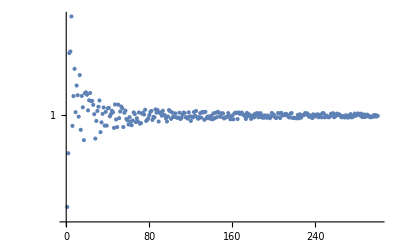

```mathematica
pts = Table[logDelta[t]/t,{t,1,300}];
ListPlot[pts,ScalingFunctions->"Log"]
```

Making a list of Standard Deviations of the Mean from each point in pts to the last point.

```mathematica
sdomlist = {};For[i=1,i<Length[pts],i++,AppendTo[sdomlist,StandardDeviation[pts[[i;;-1]]]/√(Length[pts[[i;;-1]]])];sdomlist]
```

Approaches the asymptote at the min of this list, so determining position & removing the curly brackets around it:

```mathematica
asympoint =Position[sdomlist,Min[sdomlist]];
asympoint = Flatten[asympoint];
asympoint = asympoint[[1]]
```

170

Finding the mean and standard deviation from the time it reaches the asymptote until the end of the list -- should be approximately 1

```mathematica
mean=Mean[pts[[asympoint;;-1]]];
std = StandardDeviation[pts[[asympoint;;-1]]];
stdom= std/Sqrt[Length[pts[[asympoint;;-1]]]];
```

```mathematica
(*Seeing if it's consistent with standard deviation*)
mean+std
mean - std

(*Seeing if it's consistent with standard deviation of the mean*)
mean+stdom
mean-stdom
```

1.00044

0.999148

0.999852

0.999739

Above -- not always consistent with SDOM -- depends on the amount of noise;

The pattern below here seems to be approaching/even around the mean.

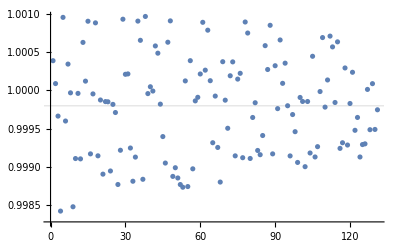

```mathematica
ListPlot[pts[[asympoint;;-1]],GridLines->{{},{mean}}]
```

The residuals:

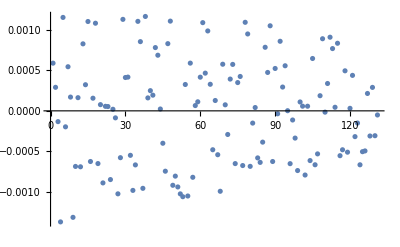

```mathematica
ListPlot[pts[[asympoint;;-1]]-mean]
```

Fitting a line to the part of the asymptote to see if it’s consistent with zero:

```mathematica
linearmodel=LinearModelFit[pts[[asympoint;;-1]],x,x];
slope = Normal[linearmodel][[2]]/x ;
slopeerr =linearmodel["ParameterErrors"][[2]];
slope - slopeerr
slope + slopeerr
```

-1.47953×10^-6

1.52206×10^-6

Slope is consistent with zero

Now, testing for a non-exponential function:

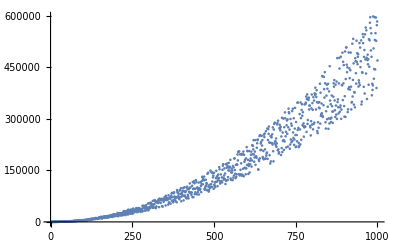

```mathematica
parpts = Table[RandomReal[{-0.25,0.25}]*(0.5x^2)+(0.5x^2),{x,1,1000}];
errparpts = parpts - Table[(0.5x^2),{x,1,1000}];
ListPlot[parpts]
```

Redefining with new parameters:

```mathematica
solList3 = parpts;
xlist3 = Table[x,{x,1,1000}];
xlist4 = Table[x,{x,1,1000}];
solList4 = ConstantArray[0,1000];
logDelta2[t_]:= Module[{deltaX, deltaY,dist},
deltaY = solList3[[t]]-solList4[[t]];
deltaX = xlist3[[t]] - xlist4[[t]] ;

dist = Sqrt[deltaX^2 + deltaY^2];
Log[dist]]
```

Same process as before:

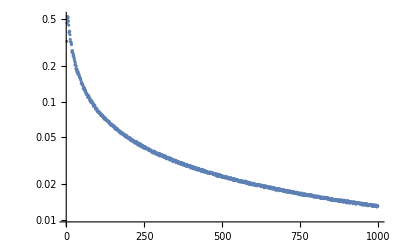

```mathematica
pts2 = Table[logDelta2[t]/t,{t,1,1000}];
ListPlot[pts2,ScalingFunctions->"Log"]
```

Making a list of standard deviations of the mean & the minimum of that list should be where it approaches the asymptote

```mathematica
sdomlist2 = {};For[i=1,i<Length[pts2],i++,AppendTo[sdomlist2,StandardDeviation[pts2[[i;;-1]]]/√(Length[pts2[[i;;-1]]])];sdomlist]
asympoint2 =Position[sdomlist2,Min[sdomlist2]];
asympoint2 = Flatten[asympoint2];
asympoint2 = asympoint2[[1]]
```

951

Should be 0:

```mathematica
mean2=Mean[pts2[[asympoint2;;-1]]];
std2 = StandardDeviation[pts2[[asympoint2;;-1]]];
stdom2 = std2/Sqrt[Length[pts2[[asympoint2;;-1]]]];
```

```mathematica
(*Testing to see if it's consistent with standard deviation*)
mean2-std2
mean2+std2

(*standard deviation of the mean*)
mean2-stdom2
mean2+stdom2
```

0.0131859

0.0136302

0.0133766

0.0134395

The values are NOT consistent with zero.

The end points seem to be trending downward:

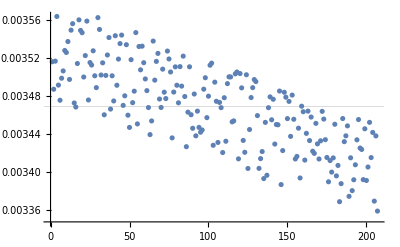

```mathematica
ListPlot[pts2[[asympoint2;;-1]],GridLines->{{},{mean2}}]
```

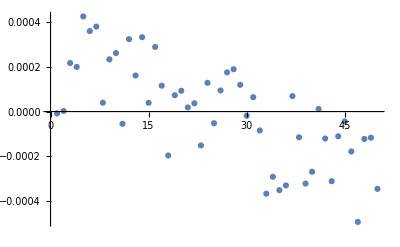

```mathematica
residuals = pts2[[asympoint2;;-1]] - mean2;
ListPlot[residuals]
```

Fitting a linear model to see if the slope is consistent with zero:

```mathematica
linearmodel2=LinearModelFit[pts2[[asympoint;;-1]],x,x];
slope2 = Normal[linearmodel2][[2]]/x ;
slopeerr2 =linearmodel2["ParameterErrors"][[2]];
slope2 - slopeerr2
slope2 + slopeerr2
```

-0.0000411077

-0.0000399235

The slope is NOT consistent with zero.

Finding a model for the function and finding its limit -- this only works here; trying this for exponential cases doesn’t work.:

```mathematica
FindFormula[pts2,x,4,All,RandomSeeding->0,SpecificityGoal->"Low"]
```

```mathematica
func2=FindFormula[pts2,x,4,RandomSeeding->0,SpecificityGoal->"Low"][[1]]
```

Piecewise[{{0.67164+0.00038294 x-2.06412×10^-8 x^2-0.132069 Log[x], 1.≤x<239.816}, {0.247167+0.0000394165 x-6.06341×10^-9 x^2-0.0386577 Log[x], 239.816≤x<2501.}, {0.0123907-3.17726×10^-6 x+2.77952×10^-10 x^2, 2501.≤x<5000.}, {0, True}}]

```mathematica
Limit[func2,x->Infinity]
```

0.